```mathematica
ΔE[n_,F_]:=-3/2 n(n-1)e a0 F/.{e:>1.6*^-19,a0:>5.29*^-11}
Energy[n_]:=-rydberg/n^2/.{rydberg:>13.6*1.6*^-19}
```

```mathematica
energyLine[n_,F_]:=Energy[n] + ΔE[n,F]
```

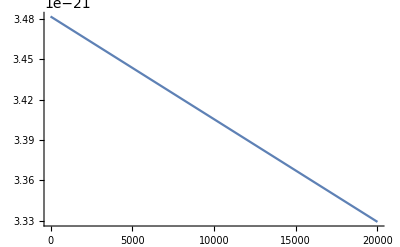

```mathematica
Plot[energyLine[25,F],{F,0,20000}]
```

```mathematica
eqn = (-Subscript[R, ∞] h c)/(n+1)^2-3/2(n+1)n e Subscript[a, 0] F == (-Subscript[R, ∞]h c)/n^2+3/2 n (n-1) e Subscript[a, 0] F
```

-3/2 e F n (1+n) a_0-(c h R_∞)/(1+n)^2==3/2 e F (-1+n) n a_0-(c h R_∞)/n^2

```mathematica
soln = F/.Solve[eqn,F][[1]]
```

(c h (1+2 n) R_∞)/(3 e n^4 (1+n)^2 a_0)

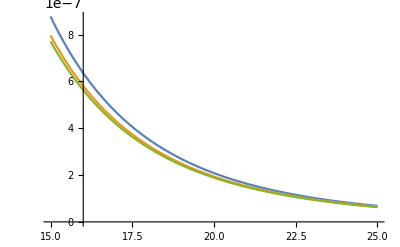

```mathematica
Plot[{2/(3 n^5),soln,orderTerm},{n,15,25}]
```

```mathematica
orderTerm = soln//Expand//Last
```

2/(3 n^3 (1+n)^2)

```mathematica
consts = {c->2.99792458*^8,h->6.62606957*^-34,e->1.60217657*^-19,Subscript[a, 0]->5.2917721092*^-11,Subscript[R, ∞]->10973731.6}
```

{c→2.99792×10^8,h→6.62607×10^-34,e→1.60218×10^-19,a_0→5.29177×10^-11,R_∞→1.09737×10^7}

```mathematica
soln/.{c->2.99792458*^8,h->6.62606957*^-34,e->1.60217657*^-19,Subscript[a, 0]->5.2917721092*^-11,Subscript[R, ∞]->10973731.6}
soln
```

(8.57034×10^10 (1+2 n))/(n^4 (1+n)^2)

(c h (1+2 n) R_∞)/(3 e n^4 (1+n)^2 a_0)

```mathematica
eqnk = (-Subscript[R, ∞] h c)/(n+1)^2-3/2(n+1)n e Subscript[a, 0] F == (-Subscript[R, ∞]h c)/n^2+3/2 n k e Subscript[a, 0] F
```

-3/2 e F n (1+n) a_0-(c h R_∞)/(1+n)^2==3/2 e F k n a_0-(c h R_∞)/n^2

```mathematica
solnk = F/.Solve[eqnk,F][[1]]
```

(2 c h (1+2 n) R_∞)/(3 e n^3 (1+n)^2 (1+k+n) a_0)

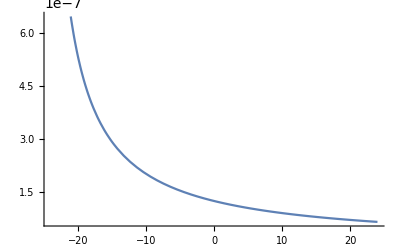

```mathematica
Plot[Evaluate[solnk/.{n->25,c->1,h->1,Subscript[R, ∞]->1,e->1,Subscript[a, 0]->1}],{k,-24,24}]
```

```mathematica
solnk/.consts
```

(1.71407×10^11 (1+2 n))/(n^3 (1+n)^2 (1+k+n))

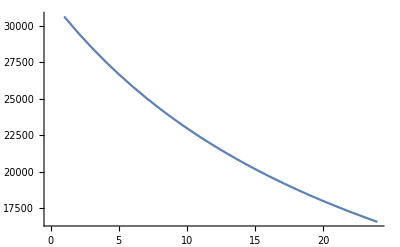

```mathematica
ListPlot[Table[solnk/.consts/.n->25,{k,1,24}],Joined->True]
```